```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Needs["ErrorBarPlots`"]
```

DropInList lässt das von einer Liste list mit inneren Listen jedes Element von from bis to fallen (jeweils inklusive)

```mathematica
DropInList[list_,from_,to_]:=Module[{buffer=list}, For[i=0,i<Length[buffer],i++;buffer[[i]]=Drop[buffer[[i]],{from,to}]];If[from⩽to,
Return[buffer],Return["It has to be from =< to"]]]
```

ErrorBarXY erzeugt eine Liste mit ErrorBar[x[[i]],y[[i]]]
Alternativ: ErrorBarXY[listXerr_,listYerr_]=ErrorBar@@@(Partition[Flatten[Riffle[listXerr,listYerr]],2])

```mathematica
ErrorBarXY[listXerr_,listYerr_]:=Module[{buffer=listXerr}, For[i=0,i<Length[buffer],i++;buffer[[i]]=ErrorBar[listXerr[[i]],listYerr[[i]]]]; If[Length[listXerr]==Length[listYerr],
Return[buffer],Return["Length of lists not equal"]]]
```

errorPlotValue erzeugt die Punkte aus listX und listY und hängt jedem Punkt die entsprechende Errorbar[listXerr,listYerr] an

```mathematica
errorPlotValue[listX_,listY_,listXerr_,listYerr_]:=Module[{buffer=listXerr,errors,points,plotValues}, errors=ErrorBarXY[listXerr,listYerr];
points=Partition[Flatten[Riffle[listX,listY]],2];
plotValues=Partition[Riffle[points,errors],2]; If[Length[listXerr]==Length[listYerr]==Length[listX]==Length[listY],
Return[plotValues],Return["Length of lists not equal"]]]
```

errorPropNew ist für die Fehlerfortpflanzung ganzer Listen geeignet. vars={{x,dx},{y,dy}...} und func eine Funktion die von x,y... abhängt. Es wird die zugehörige Fehlerfunktion zurückgegeben. Speicher diese unter einem Namen ab zB errFkt.
Nutze errFkt[f, list_x,list_dx,list_y,list_dy,...]

```mathematica
errorPropNew[func_,vars_]:=Module[{derivs=Table[0,{Length[vars]}],funcErrorForm,parameter,errFunction},

For[ii=1,ii≤Length[vars],ii++,derivs[[ii]]=D[func,vars[[ii,1]]];];
parameter=Flatten[vars];
funcErrorForm=Sqrt[Sum[(derivs[[ii]]*vars[[ii,2]])^2,{ii,Length[vars]}]];
errFunction=Function@@{parameter,funcErrorForm};
Return[errFunction];];
```

Wendet f auf die n-te Komponenten jedes Punktes in g an. Alternativ {f@First[#], Last[#]} &/@ g;

```mathematica
(*  MapAt[(f[#])&,#,1]&/@g   *)
```

C16

## M2 n-dotiert

### I=20mA n-dotiert

```mathematica
messwerteM2n=({{26.1, 30.0, 35.0, 40.0, 45.0, 50.3, 55.0, 60.0, 65.0, 70.0, 75.0, 80.0, 85.0, 90.0, 95.0, 100.3, 105.0, 110.0, 115.3, 120.0, 125.0, 130.0, 135.0, 140.0, 145.0, 150.5, 155.0, 160.0, 165.6, 170.0}, {.764, .759, .797, .806, .832, .850, .828, .791, .835, .796, .864, .781, .732, .706, .690, .666, .551, .512, .472, .486, .437, .390, .349, .312, .279, .245, .223, .199, .176, .160}})
```

{{26.1,30.,35.,40.,45.,50.3,55.,60.,65.,70.,75.,80.,85.,90.,95.,100.3,105.,110.,115.3,120.,125.,130.,135.,140.,145.,150.5,155.,160.,165.6,170.},{0.764,0.759,0.797,0.806,0.832,0.85,0.828,0.791,0.835,0.796,0.864,0.781,0.732,0.706,0.69,0.666,0.551,0.512,0.472,0.486,0.437,0.39,0.349,0.312,0.279,0.245,0.223,0.199,0.176,0.16}}

```mathematica
c=20 *10^-3;
b=10*10^-3;
d=1*10^-3;
```

```mathematica
iM2n=20.0*10^-3;
```

```mathematica
diM2n=1.0*10^-3;
```

```mathematica
kB=1.3806504*^-23 ;
```

```mathematica
f[x_]:=x+273.15;
```

```mathematica
messwerteM2nt=Transpose[messwerteM2n] ;
```

```mathematica
messwerteM2nsi=MapAt[(f[#])&,#,1]&/@messwerteM2nt
```

{{299.25,0.764},{303.15,0.759},{308.15,0.797},{313.15,0.806},{318.15,0.832},{323.45,0.85},{328.15,0.828},{333.15,0.791},{338.15,0.835},{343.15,0.796},{348.15,0.864},{353.15,0.781},{358.15,0.732},{363.15,0.706},{368.15,0.69},{373.45,0.666},{378.15,0.551},{383.15,0.512},{388.45,0.472},{393.15,0.486},{398.15,0.437},{403.15,0.39},{408.15,0.349},{413.15,0.312},{418.15,0.279},{423.65,0.245},{428.15,0.223},{433.15,0.199},{438.75,0.176},{443.15,0.16}}

```mathematica
messwerteM2nsi //MatrixForm
```

(299.25 | 0.764
303.15 | 0.759
308.15 | 0.797
313.15 | 0.806
318.15 | 0.832
323.45 | 0.85
328.15 | 0.828
333.15 | 0.791
338.15 | 0.835
343.15 | 0.796
348.15 | 0.864
353.15 | 0.781
358.15 | 0.732
363.15 | 0.706
368.15 | 0.69
373.45 | 0.666
378.15 | 0.551
383.15 | 0.512
388.45 | 0.472
393.15 | 0.486
398.15 | 0.437
403.15 | 0.39
408.15 | 0.349
413.15 | 0.312
418.15 | 0.279
423.65 | 0.245
428.15 | 0.223
433.15 | 0.199
438.75 | 0.176
443.15 | 0.16)

```mathematica
uM2n=Transpose[messwerteM2nsi][[2]]
```

{0.764,0.759,0.797,0.806,0.832,0.85,0.828,0.791,0.835,0.796,0.864,0.781,0.732,0.706,0.69,0.666,0.551,0.512,0.472,0.486,0.437,0.39,0.349,0.312,0.279,0.245,0.223,0.199,0.176,0.16}

```mathematica
leitfM2n[U_]:=iM2n/U*c/(b *d);
```

```mathematica
leitfM2n=leitfM2n[#]&/@uM2n
```

{52.356,52.7009,50.1882,49.6278,48.0769,47.0588,48.3092,50.5689,47.9042,50.2513,46.2963,51.2164,54.6448,56.6572,57.971,60.0601,72.5953,78.125,84.7458,82.3045,91.5332,102.564,114.613,128.205,143.369,163.265,179.372,201.005,227.273,250.}

```mathematica
g[x_]:=Log[x];
```

```mathematica
leitfM2nln=g[#]&/@leitfM2n
```

{3.95807,3.96463,3.91578,3.90455,3.8728,3.8514,3.87762,3.92334,3.8692,3.91704,3.83506,3.93606,4.00085,4.03702,4.05994,4.09535,4.2849,4.35831,4.43966,4.41043,4.5167,4.63049,4.74156,4.85363,4.96542,5.09538,5.18946,5.30333,5.42615,5.52146}

```mathematica
g1[x_]:=1/(2 kB x);
```

```mathematica
messwerteM2nxaxis=g1[#]&/@Transpose[messwerteM2nsi][[1]]
```

{1.21019×10^20,1.19462×10^20,1.17523×10^20,1.15647×10^20,1.13829×10^20,1.11964×10^20,1.10361×10^20,1.08704×10^20,1.07097×10^20,1.05536×10^20,1.04021×10^20,1.02548×10^20,1.01116×10^20,9.97241×10^19,9.83697×10^19,9.69737×10^19,9.57684×10^19,9.45186×10^19,9.3229×10^19,9.21145×10^19,9.09577×10^19,8.98296×10^19,8.87292×10^19,8.76554×10^19,8.66072×10^19,8.54829×10^19,8.45844×10^19,8.3608×10^19,8.25409×10^19,8.17213×10^19}

### Fehler

4 stellig U bis 9.999V Auflösung 0.001V Fehler (.5% + 3dgts)

```mathematica
messfehler1u[x_]:=0.001*3+x*0.005;
```

```mathematica
fehlerM2nU=messfehler1u[#] & /@ uM2n
```

{0.00682,0.006795,0.006985,0.00703,0.00716,0.00725,0.00714,0.006955,0.007175,0.00698,0.00732,0.006905,0.00666,0.00653,0.00645,0.00633,0.005755,0.00556,0.00536,0.00543,0.005185,0.00495,0.004745,0.00456,0.004395,0.004225,0.004115,0.003995,0.00388,0.0038}

```mathematica
errorPropNew[Log[I1/U*c/(b *d)],{{U,dU},{I1,dI1}}]
```

Function[{U,dU,I1,dI1},√(dI1^2/I1^2+dU^2/U^2)]

```mathematica
errorPropNew[I1/U*c/(b *d),{{U,dU},{I1,dI1}}]
```

Function[{U,dU,I1,dI1},√((4000000 dU^2 I1^2)/U^4+(4000000 dI1^2)/U^2)]

```mathematica
leitfM2nErr=errorPropNew[I1/U*c/(b *d),{{U,dU},{I1,dI1}}]@@{uM2n,fehlerM2nU,iM2n,diM2n}
```

{2.65919,2.67695,2.54767,2.51886,2.43919,2.38693,2.45112,2.56724,2.43032,2.55091,2.34781,2.60055,2.77711,2.88092,2.94877,3.05678,3.70811,3.99732,4.3452,4.21672,4.70375,5.29085,5.93874,6.6785,7.51581,8.63516,9.5599,10.8301,12.4192,13.8385}

```mathematica
leitfM2nlnErr=errorPropNew[Log[I1/U*c/(b *d)],{{U,dU},{I1,dI1}}]@@{uM2n,fehlerM2nU,iM2n,diM2n}
```

{0.0507906,0.0507952,0.0507623,0.050755,0.0507352,0.0507223,0.0507381,0.0507672,0.050733,0.0507631,0.0507127,0.0507757,0.0508211,0.0508483,0.0508663,0.0508953,0.0510793,0.0511657,0.0512734,0.0512331,0.0513885,0.0515858,0.0518155,0.0520923,0.0524228,0.0528903,0.0532964,0.0538797,0.0546443,0.055354}

```mathematica
messfehler1T[x_]:=3+x*0.02;
```

```mathematica
TM2nGradErr=messfehler1T[#] & /@messwerteM2n[[1]]
```

{3.522,3.6,3.7,3.8,3.9,4.006,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.006,5.1,5.2,5.306,5.4,5.5,5.6,5.7,5.8,5.9,6.01,6.1,6.2,6.312,6.4}

```mathematica
errorPropNew[1/(2 kB t),{{t,dt}}]
```

Function[{t,dt},3.62148×10^22 √(dt^2/t^4)]

```mathematica
TM2nK=Transpose[messwerteM2nsi][[1]]
```

{299.25,303.15,308.15,313.15,318.15,323.45,328.15,333.15,338.15,343.15,348.15,353.15,358.15,363.15,368.15,373.45,378.15,383.15,388.45,393.15,398.15,403.15,408.15,413.15,418.15,423.65,428.15,433.15,438.75,443.15}

```mathematica
messwerteM2nxaxisErr=errorPropNew[1/(2 kB t),{{t,dt}}]@@{TM2nK,TM2nGradErr}
```

{1.42432×10^18,1.41864×10^18,1.41112×10^18,1.40335×10^18,1.39536×10^18,1.3867×10^18,1.37888×10^18,1.37043×10^18,1.36187×10^18,1.35323×10^18,1.34452×10^18,1.33575×10^18,1.32695×10^18,1.31812×10^18,1.30928×10^18,1.29991×10^18,1.2916×10^18,1.28278×10^18,1.27345×10^18,1.26521×10^18,1.25648×10^18,1.24779×10^18,1.23914×10^18,1.23055×10^18,1.22201×10^18,1.21268×10^18,1.2051×10^18,1.19674×10^18,1.18746×10^18,1.18022×10^18}

### Plotten (Vorbereitung)

```mathematica
pointsM2n=Partition[Flatten[Riffle[messwerteM2nxaxis,leitfM2nln]],2];
```

```mathematica
Length[messwerteM2nxaxis]
```

30

```mathematica
errorsM2n=Table[ErrorBar[messwerteM2nxaxisErr[[i ]],leitfM2nlnErr[[i]]],{i,1,30}]
```

{ErrorBar[1.42432×10^18,0.0507906],ErrorBar[1.41864×10^18,0.0507952],ErrorBar[1.41112×10^18,0.0507623],ErrorBar[1.40335×10^18,0.050755],ErrorBar[1.39536×10^18,0.0507352],ErrorBar[1.3867×10^18,0.0507223],ErrorBar[1.37888×10^18,0.0507381],ErrorBar[1.37043×10^18,0.0507672],ErrorBar[1.36187×10^18,0.050733],ErrorBar[1.35323×10^18,0.0507631],ErrorBar[1.34452×10^18,0.0507127],ErrorBar[1.33575×10^18,0.0507757],ErrorBar[1.32695×10^18,0.0508211],ErrorBar[1.31812×10^18,0.0508483],ErrorBar[1.30928×10^18,0.0508663],ErrorBar[1.29991×10^18,0.0508953],ErrorBar[1.2916×10^18,0.0510793],ErrorBar[1.28278×10^18,0.0511657],ErrorBar[1.27345×10^18,0.0512734],ErrorBar[1.26521×10^18,0.0512331],ErrorBar[1.25648×10^18,0.0513885],ErrorBar[1.24779×10^18,0.0515858],ErrorBar[1.23914×10^18,0.0518155],ErrorBar[1.23055×10^18,0.0520923],ErrorBar[1.22201×10^18,0.0524228],ErrorBar[1.21268×10^18,0.0528903],ErrorBar[1.2051×10^18,0.0532964],ErrorBar[1.19674×10^18,0.0538797],ErrorBar[1.18746×10^18,0.0546443],ErrorBar[1.18022×10^18,0.055354]}

```mathematica
plotValuesM2n=Partition[Riffle[pointsM2n,errorsM2n],2]
```

{{{1.21019×10^20,3.95807},ErrorBar[1.42432×10^18,0.0507906]},{{1.19462×10^20,3.96463},ErrorBar[1.41864×10^18,0.0507952]},{{1.17523×10^20,3.91578},ErrorBar[1.41112×10^18,0.0507623]},{{1.15647×10^20,3.90455},ErrorBar[1.40335×10^18,0.050755]},{{1.13829×10^20,3.8728},ErrorBar[1.39536×10^18,0.0507352]},{{1.11964×10^20,3.8514},ErrorBar[1.3867×10^18,0.0507223]},{{1.10361×10^20,3.87762},ErrorBar[1.37888×10^18,0.0507381]},{{1.08704×10^20,3.92334},ErrorBar[1.37043×10^18,0.0507672]},{{1.07097×10^20,3.8692},ErrorBar[1.36187×10^18,0.050733]},{{1.05536×10^20,3.91704},ErrorBar[1.35323×10^18,0.0507631]},{{1.04021×10^20,3.83506},ErrorBar[1.34452×10^18,0.0507127]},{{1.02548×10^20,3.93606},ErrorBar[1.33575×10^18,0.0507757]},{{1.01116×10^20,4.00085},ErrorBar[1.32695×10^18,0.0508211]},{{9.97241×10^19,4.03702},ErrorBar[1.31812×10^18,0.0508483]},{{9.83697×10^19,4.05994},ErrorBar[1.30928×10^18,0.0508663]},{{9.69737×10^19,4.09535},ErrorBar[1.29991×10^18,0.0508953]},{{9.57684×10^19,4.2849},ErrorBar[1.2916×10^18,0.0510793]},{{9.45186×10^19,4.35831},ErrorBar[1.28278×10^18,0.0511657]},{{9.3229×10^19,4.43966},ErrorBar[1.27345×10^18,0.0512734]},{{9.21145×10^19,4.41043},ErrorBar[1.26521×10^18,0.0512331]},{{9.09577×10^19,4.5167},ErrorBar[1.25648×10^18,0.0513885]},{{8.98296×10^19,4.63049},ErrorBar[1.24779×10^18,0.0515858]},{{8.87292×10^19,4.74156},ErrorBar[1.23914×10^18,0.0518155]},{{8.76554×10^19,4.85363},ErrorBar[1.23055×10^18,0.0520923]},{{8.66072×10^19,4.96542},ErrorBar[1.22201×10^18,0.0524228]},{{8.54829×10^19,5.09538},ErrorBar[1.21268×10^18,0.0528903]},{{8.45844×10^19,5.18946},ErrorBar[1.2051×10^18,0.0532964]},{{8.3608×10^19,5.30333},ErrorBar[1.19674×10^18,0.0538797]},{{8.25409×10^19,5.42615},ErrorBar[1.18746×10^18,0.0546443]},{{8.17213×10^19,5.52146},ErrorBar[1.18022×10^18,0.055354]}}

```mathematica
BoltzmannConstant
```

(1.38065×10^-23 Joule)/Kelvin

```mathematica
errPlotM2n=ErrorListPlot[plotValuesM2n,AxesLabel->{"1/(2 SubscriptBox[k, B] T) in 1/J","ln(σ) inA/(V m)"},PlotRange->Full,PlotStyle-> {Darker[Blue]}]
```

-Graphics-

```mathematica
messwerteM2nxaxisErr/messwerteM2nxaxis
```

{0.0117694,0.0118753,0.0120071,0.0121348,0.0122584,0.0123852,0.0124943,0.0126069,0.0127163,0.0128224,0.0129255,0.0130256,0.013123,0.0132177,0.0133098,0.0134047,0.0134867,0.0135717,0.0136594,0.0137352,0.0138139,0.0138906,0.0139655,0.0140385,0.0141098,0.0141862,0.0142473,0.0143137,0.0143863,0.0144421}

```mathematica
leitfM2nlnErr/leitfM2nln
```

{0.0128322,0.0128121,0.0129635,0.0129989,0.0131004,0.0131698,0.0130849,0.0129398,0.013112,0.0129596,0.0132234,0.0129001,0.0127026,0.0125955,0.0125288,0.0124276,0.0119208,0.0117398,0.0115489,0.0116164,0.0113774,0.0111405,0.0109279,0.0107326,0.0105576,0.0103801,0.0102701,0.0101596,0.0100706,0.0100252}

### Plotten (Vorbereitung) Leitfähigkeit gegen T

```mathematica
pointsM2n1=Partition[Flatten[Riffle[TM2nK,leitfM2n]],2];
```

```mathematica
Length[TM2nK]
```

30

```mathematica
errorsM2n1=Table[ErrorBar[TM2nGradErr[[i ]],leitfM2nErr[[i]]],{i,1,30}]
```

{ErrorBar[3.522,2.65919],ErrorBar[3.6,2.67695],ErrorBar[3.7,2.54767],ErrorBar[3.8,2.51886],ErrorBar[3.9,2.43919],ErrorBar[4.006,2.38693],ErrorBar[4.1,2.45112],ErrorBar[4.2,2.56724],ErrorBar[4.3,2.43032],ErrorBar[4.4,2.55091],ErrorBar[4.5,2.34781],ErrorBar[4.6,2.60055],ErrorBar[4.7,2.77711],ErrorBar[4.8,2.88092],ErrorBar[4.9,2.94877],ErrorBar[5.006,3.05678],ErrorBar[5.1,3.70811],ErrorBar[5.2,3.99732],ErrorBar[5.306,4.3452],ErrorBar[5.4,4.21672],ErrorBar[5.5,4.70375],ErrorBar[5.6,5.29085],ErrorBar[5.7,5.93874],ErrorBar[5.8,6.6785],ErrorBar[5.9,7.51581],ErrorBar[6.01,8.63516],ErrorBar[6.1,9.5599],ErrorBar[6.2,10.8301],ErrorBar[6.312,12.4192],ErrorBar[6.4,13.8385]}

```mathematica
plotValuesM2n1=Partition[Riffle[pointsM2n1,errorsM2n1],2]
```

{{{299.25,52.356},ErrorBar[3.522,2.65919]},{{303.15,52.7009},ErrorBar[3.6,2.67695]},{{308.15,50.1882},ErrorBar[3.7,2.54767]},{{313.15,49.6278},ErrorBar[3.8,2.51886]},{{318.15,48.0769},ErrorBar[3.9,2.43919]},{{323.45,47.0588},ErrorBar[4.006,2.38693]},{{328.15,48.3092},ErrorBar[4.1,2.45112]},{{333.15,50.5689},ErrorBar[4.2,2.56724]},{{338.15,47.9042},ErrorBar[4.3,2.43032]},{{343.15,50.2513},ErrorBar[4.4,2.55091]},{{348.15,46.2963},ErrorBar[4.5,2.34781]},{{353.15,51.2164},ErrorBar[4.6,2.60055]},{{358.15,54.6448},ErrorBar[4.7,2.77711]},{{363.15,56.6572},ErrorBar[4.8,2.88092]},{{368.15,57.971},ErrorBar[4.9,2.94877]},{{373.45,60.0601},ErrorBar[5.006,3.05678]},{{378.15,72.5953},ErrorBar[5.1,3.70811]},{{383.15,78.125},ErrorBar[5.2,3.99732]},{{388.45,84.7458},ErrorBar[5.306,4.3452]},{{393.15,82.3045},ErrorBar[5.4,4.21672]},{{398.15,91.5332},ErrorBar[5.5,4.70375]},{{403.15,102.564},ErrorBar[5.6,5.29085]},{{408.15,114.613},ErrorBar[5.7,5.93874]},{{413.15,128.205},ErrorBar[5.8,6.6785]},{{418.15,143.369},ErrorBar[5.9,7.51581]},{{423.65,163.265},ErrorBar[6.01,8.63516]},{{428.15,179.372},ErrorBar[6.1,9.5599]},{{433.15,201.005},ErrorBar[6.2,10.8301]},{{438.75,227.273},ErrorBar[6.312,12.4192]},{{443.15,250.},ErrorBar[6.4,13.8385]}}

```mathematica
BoltzmannConstant
```

(1.38065×10^-23 Joule)/Kelvin

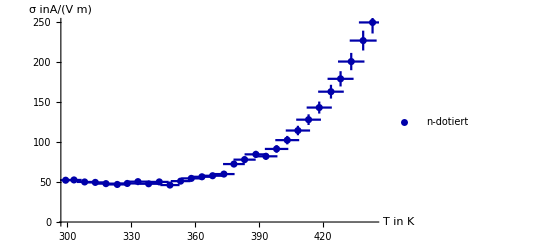

```mathematica
errPlotM2n1=ErrorListPlot[plotValuesM2n1,AxesLabel->{"T in  K","σ inA/(V m)"},PlotRange->Full,PlotStyle-> {Darker[Blue]},PlotLegends->Placed[{"n-dotiert"},{.25,.65}]]
```

```mathematica
TM2nGradErr/TM2nK
```

{0.0117694,0.0118753,0.0120071,0.0121348,0.0122584,0.0123852,0.0124943,0.0126069,0.0127163,0.0128224,0.0129255,0.0130256,0.013123,0.0132177,0.0133098,0.0134047,0.0134867,0.0135717,0.0136594,0.0137352,0.0138139,0.0138906,0.0139655,0.0140385,0.0141098,0.0141862,0.0142473,0.0143137,0.0143863,0.0144421}

```mathematica
leitfM2nErr/leitfM2n
```

{0.0507906,0.0507952,0.0507623,0.050755,0.0507352,0.0507223,0.0507381,0.0507672,0.050733,0.0507631,0.0507127,0.0507757,0.0508211,0.0508483,0.0508663,0.0508953,0.0510793,0.0511657,0.0512734,0.0512331,0.0513885,0.0515858,0.0518155,0.0520923,0.0524228,0.0528903,0.0532964,0.0538797,0.0546443,0.055354}

## M2

### I=20mA p-dotiert

```mathematica
messwerteM2p=({{25.8, 41.4, 51.3, 59.2, 80.2, 92.4, 101.8, 110.3, 118.2, 129.3, 132.9, 148.5, 163.1}, {.880, .980, 1.040, 1.040, 1.018, 0.929, .704, .698, .632, .469, .360, .282, .195}})
```

{{25.8,41.4,51.3,59.2,80.2,92.4,101.8,110.3,118.2,129.3,132.9,148.5,163.1},{0.88,0.98,1.04,1.04,1.018,0.929,0.704,0.698,0.632,0.469,0.36,0.282,0.195}}

```mathematica
c=20 *10^-3;
b=10*10^-3;
d=1*10^-3;
```

```mathematica
iM2p=20.0*10^-3;
```

```mathematica
diM2p=1.0*10^-3;
```

```mathematica
kB=1.3806504*^-23 ;
```

```mathematica
f[x_]:=x+273.15;
```

```mathematica
messwerteM2pt=Transpose[messwerteM2p] ;
```

```mathematica
messwerteM2psi=MapAt[(f[#])&,#,1]&/@messwerteM2pt
```

{{298.95,0.88},{314.55,0.98},{324.45,1.04},{332.35,1.04},{353.35,1.018},{365.55,0.929},{374.95,0.704},{383.45,0.698},{391.35,0.632},{402.45,0.469},{406.05,0.36},{421.65,0.282},{436.25,0.195}}

```mathematica
messwerteM2psi //MatrixForm
```

(298.95 | 0.88
314.55 | 0.98
324.45 | 1.04
332.35 | 1.04
353.35 | 1.018
365.55 | 0.929
374.95 | 0.704
383.45 | 0.698
391.35 | 0.632
402.45 | 0.469
406.05 | 0.36
421.65 | 0.282
436.25 | 0.195)

```mathematica
uM2p=Transpose[messwerteM2psi][[2]]
```

{0.88,0.98,1.04,1.04,1.018,0.929,0.704,0.698,0.632,0.469,0.36,0.282,0.195}

```mathematica
leitfM2p[U_]:=iM2p/U*c/(b *d);
```

```mathematica
leitfM2p=leitfM2p[#]&/@uM2p
```

{45.4545,40.8163,38.4615,38.4615,39.2927,43.0571,56.8182,57.3066,63.2911,85.2878,111.111,141.844,205.128}

```mathematica
g[x_]:=Log[x];
```

```mathematica
leitfM2pln=g[#]&/@leitfM2p
```

{3.81671,3.70908,3.64966,3.64966,3.67104,3.76253,4.03986,4.04842,4.14775,4.44603,4.71053,4.95473,5.32364}

```mathematica
g1[x_]:=1/(2 kB x);
```

```mathematica
messwerteM2pxaxis=g1[#]&/@Transpose[messwerteM2psi][[1]]
```

{1.2114×10^20,1.15132×10^20,1.11619×10^20,1.08966×10^20,1.0249×10^20,9.90694×10^19,9.65857×10^19,9.44447×10^19,9.25382×10^19,8.99859×10^19,8.91881×10^19,8.58883×10^19,8.30139×10^19}

### Fehler

4 stellig U bis 9.999V Auflösung 0.001V Fehler (.5% + 3dgts)

```mathematica
messfehler1u[x_]:=0.001*3+x*0.005;
```

```mathematica
fehlerM2pU=messfehler1u[#] & /@ uM2p
```

{0.0074,0.0079,0.0082,0.0082,0.00809,0.007645,0.00652,0.00649,0.00616,0.005345,0.0048,0.00441,0.003975}

```mathematica
errorPropNew[Log[I1/U*c/(b *d)],{{U,dU},{I1,dI1}}]
```

Function[{U,dU,I1,dI1},√(dI1^2/I1^2+dU^2/U^2)]

```mathematica
errorPropNew[I1/U*c/(b *d),{{U,dU},{I1,dI1}}]
```

Function[{U,dU,I1,dI1},√((4000000 dU^2 I1^2)/U^4+(4000000 dI1^2)/U^2)]

```mathematica
leitfM2pErr=errorPropNew[I1/U*c/(b *d),{{U,dU},{I1,dI1}}]@@{uM2p,fehlerM2pU,iM2p,diM2p}
```

{2.30465,2.06717,1.94684,1.94684,1.9893,2.18182,2.88923,2.91445,3.22412,4.37376,5.74969,7.43099,11.076}

```mathematica
leitfM2plnErr=errorPropNew[Log[I1/U*c/(b *d)],{{U,dU},{I1,dI1}}]@@{uM2p,fehlerM2pU,iM2p,diM2p}
```

{0.0507022,0.0506457,0.0506179,0.0506179,0.0506276,0.0506727,0.0508505,0.0508572,0.0509412,0.0512824,0.0517472,0.0523885,0.0539957}

```mathematica
messfehler1T[x_]:=3+x*0.02;
```

```mathematica
TM2pGradErr=messfehler1T[#] & /@messwerteM2p[[1]]
```

{3.516,3.828,4.026,4.184,4.604,4.848,5.036,5.206,5.364,5.586,5.658,5.97,6.262}

```mathematica
errorPropNew[1/(2 kB t),{{t,dt}}]
```

Function[{t,dt},3.62148×10^22 √(dt^2/t^4)]

```mathematica
TM2pK=Transpose[messwerteM2psi][[1]]
```

{298.95,314.55,324.45,332.35,353.35,365.55,374.95,383.45,391.35,402.45,406.05,421.65,436.25}

```mathematica
messwerteM2pxaxisErr=errorPropNew[1/(2 kB t),{{t,dt}}]@@{TM2pK,TM2pGradErr}
```

{1.42475×10^18,1.40113×10^18,1.38505×10^18,1.37179×10^18,1.3354×10^18,1.31388×10^18,1.29725×10^18,1.28225×10^18,1.26837×10^18,1.249×10^18,1.24277×10^18,1.21606×10^18,1.19159×10^18}

### Plotten (Vorbereitung)

```mathematica
pointsM2p=Partition[Flatten[Riffle[messwerteM2pxaxis,leitfM2pln]],2];
```

```mathematica
Length[messwerteM2pxaxis]
```

13

```mathematica
errorsM2p=Table[ErrorBar[messwerteM2pxaxisErr[[i ]],leitfM2plnErr[[i]]],{i,1,13}]
```

{ErrorBar[1.42475×10^18,0.0507022],ErrorBar[1.40113×10^18,0.0506457],ErrorBar[1.38505×10^18,0.0506179],ErrorBar[1.37179×10^18,0.0506179],ErrorBar[1.3354×10^18,0.0506276],ErrorBar[1.31388×10^18,0.0506727],ErrorBar[1.29725×10^18,0.0508505],ErrorBar[1.28225×10^18,0.0508572],ErrorBar[1.26837×10^18,0.0509412],ErrorBar[1.249×10^18,0.0512824],ErrorBar[1.24277×10^18,0.0517472],ErrorBar[1.21606×10^18,0.0523885],ErrorBar[1.19159×10^18,0.0539957]}

```mathematica
plotValuesM2p=Partition[Riffle[pointsM2p,errorsM2p],2]
```

{{{1.2114×10^20,3.81671},ErrorBar[1.42475×10^18,0.0507022]},{{1.15132×10^20,3.70908},ErrorBar[1.40113×10^18,0.0506457]},{{1.11619×10^20,3.64966},ErrorBar[1.38505×10^18,0.0506179]},{{1.08966×10^20,3.64966},ErrorBar[1.37179×10^18,0.0506179]},{{1.0249×10^20,3.67104},ErrorBar[1.3354×10^18,0.0506276]},{{9.90694×10^19,3.76253},ErrorBar[1.31388×10^18,0.0506727]},{{9.65857×10^19,4.03986},ErrorBar[1.29725×10^18,0.0508505]},{{9.44447×10^19,4.04842},ErrorBar[1.28225×10^18,0.0508572]},{{9.25382×10^19,4.14775},ErrorBar[1.26837×10^18,0.0509412]},{{8.99859×10^19,4.44603},ErrorBar[1.249×10^18,0.0512824]},{{8.91881×10^19,4.71053},ErrorBar[1.24277×10^18,0.0517472]},{{8.58883×10^19,4.95473},ErrorBar[1.21606×10^18,0.0523885]},{{8.30139×10^19,5.32364},ErrorBar[1.19159×10^18,0.0539957]}}

```mathematica
BoltzmannConstant
```

(1.38065×10^-23 Joule)/Kelvin

```mathematica
errPlotM2p=ErrorListPlot[plotValuesM2p,AxesLabel->{"1/(2 SubscriptBox[k, B] T) in 1/J","ln(σ) inA/(V m)"},PlotRange->Full,PlotStyle-> {Darker[Red]}]
```

-Graphics-

```mathematica
messwerteM2pxaxisErr/messwerteM2pxaxis
```

{0.0117612,0.0121698,0.0124087,0.0125891,0.0130296,0.0132622,0.0134311,0.0135767,0.0137064,0.01388,0.0139342,0.0141587,0.0143542}

```mathematica
leitfM2plnErr/leitfM2pln
```

{0.0132843,0.0136545,0.0138692,0.0138692,0.0137911,0.0134677,0.0125872,0.0125622,0.0122816,0.0115344,0.0109854,0.0105734,0.0101426}

### Plotten (Vorbereitung) Leitfähigkeit gegen T

```mathematica
pointsM2p1=Partition[Flatten[Riffle[TM2pK,leitfM2p]],2];
```

```mathematica
Length[TM2pK]
```

13

```mathematica
errorsM2p1=Table[ErrorBar[TM2pGradErr[[i ]],leitfM2pErr[[i]]],{i,1,13}]
```

{ErrorBar[3.516,2.30465],ErrorBar[3.828,2.06717],ErrorBar[4.026,1.94684],ErrorBar[4.184,1.94684],ErrorBar[4.604,1.9893],ErrorBar[4.848,2.18182],ErrorBar[5.036,2.88923],ErrorBar[5.206,2.91445],ErrorBar[5.364,3.22412],ErrorBar[5.586,4.37376],ErrorBar[5.658,5.74969],ErrorBar[5.97,7.43099],ErrorBar[6.262,11.076]}

```mathematica
plotValuesM2p1=Partition[Riffle[pointsM2p1,errorsM2p1],2]
```

{{{298.95,45.4545},ErrorBar[3.516,2.30465]},{{314.55,40.8163},ErrorBar[3.828,2.06717]},{{324.45,38.4615},ErrorBar[4.026,1.94684]},{{332.35,38.4615},ErrorBar[4.184,1.94684]},{{353.35,39.2927},ErrorBar[4.604,1.9893]},{{365.55,43.0571},ErrorBar[4.848,2.18182]},{{374.95,56.8182},ErrorBar[5.036,2.88923]},{{383.45,57.3066},ErrorBar[5.206,2.91445]},{{391.35,63.2911},ErrorBar[5.364,3.22412]},{{402.45,85.2878},ErrorBar[5.586,4.37376]},{{406.05,111.111},ErrorBar[5.658,5.74969]},{{421.65,141.844},ErrorBar[5.97,7.43099]},{{436.25,205.128},ErrorBar[6.262,11.076]}}

```mathematica
BoltzmannConstant
```

(1.38065×10^-23 Joule)/Kelvin

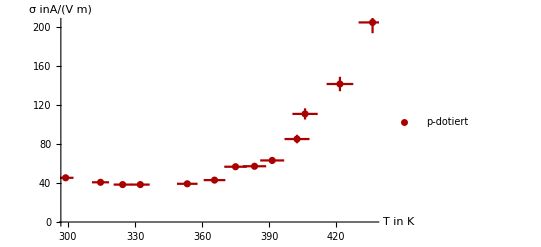

```mathematica
errPlotM2p1=ErrorListPlot[plotValuesM2p1,AxesLabel->{"T in  K","σ inA/(V m)"},PlotRange->Full,PlotStyle-> {Darker[Red]},PlotLegends->Placed[{"p-dotiert"},{.25,.75}]]
```

```mathematica
TM2pGradErr/TM2pK
```

{0.0117612,0.0121698,0.0124087,0.0125891,0.0130296,0.0132622,0.0134311,0.0135767,0.0137064,0.01388,0.0139342,0.0141587,0.0143542}

```mathematica
leitfM2pErr/leitfM2p
```

{0.0507022,0.0506457,0.0506179,0.0506179,0.0506276,0.0506727,0.0508505,0.0508572,0.0509412,0.0512824,0.0517472,0.0523885,0.0539957}

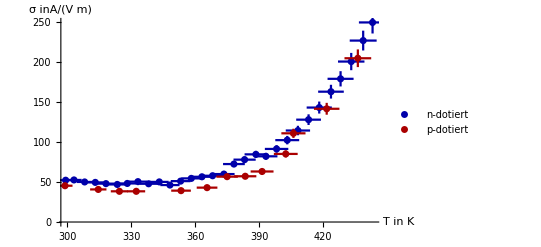

```mathematica
Show[errPlotM2n1,errPlotM2p1]
```